## Rigidity matrices

```mathematica
m=randomCellNetwork[56];//Timing
```

{1.32922,Null}

```mathematica
mechanismEnergy[m];//Timing
```

{0.028238,Null}

```mathematica
constraintEquations[m,1];//Timing
```

{0.144806,Null}

```mathematica
constraintMatrix[m]//Timing
```

{0.129293,SparseArray[…]}

```mathematica
zeroModes[m];//Timing
```

{0.189483,Null}

```mathematica
selfStresses[m];//Timing
```

{0.186274,Null}

```mathematica
infinitesimalMotions[m];//Timing
```

{0.555858,Null}

## Graphics display speed

### 2D network

```mathematica
m0=randomTriangulatedNetwork[100];
```

```mathematica
t=AbsoluteTime[];
m0
Print[AbsoluteTime[]-t]
```

-Graphics-

0.25298

```mathematica
t=AbsoluteTime[];
tmp=toGraphicsComplex[m0];
Print[AbsoluteTime[]-t]
Graphics@tmp
Print[AbsoluteTime[]-t]
```

0.455584

-Graphics-

1.80362

```mathematica
t=AbsoluteTime[];
tmp=mechanismPrimitives[m0];
Print[AbsoluteTime[]-t]
Graphics@tmp
Print[AbsoluteTime[]-t]
```

0.17475

-Graphics-

0.20603

```mathematica
t=AbsoluteTime[];
plotMechanism[m0]
AbsoluteTime[]-t
```

-Graphics-

0.20837

### 2D origami fold patterns

```mathematica
m0=randomOrigami[70];
```

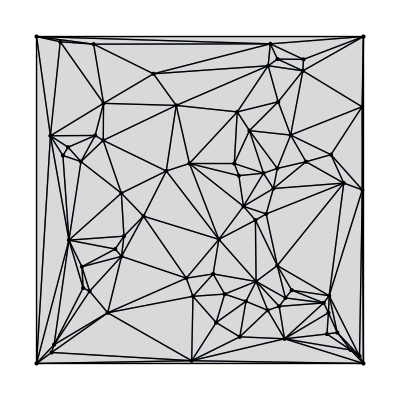

0.048863

```mathematica
t=AbsoluteTime[];
m0
Print[AbsoluteTime[]-t]
```

0.06477

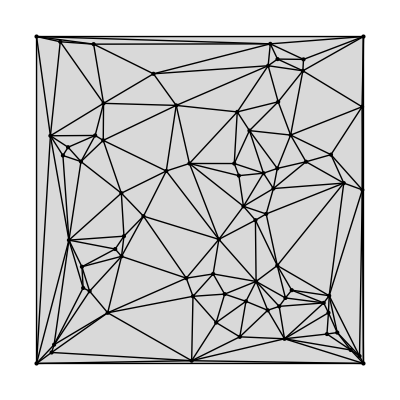

0.10576

```mathematica
t=AbsoluteTime[];
tmp=toGraphicsComplex[m0];
Print[AbsoluteTime[]-t]
Graphics@tmp
Print[AbsoluteTime[]-t]
```

```mathematica
t=AbsoluteTime[];
tmp=mechanismPrimitives[m0];
Print[AbsoluteTime[]-t]
Graphics@tmp
Print[AbsoluteTime[]-t]
```

0.0181

-Graphics-

0.063102

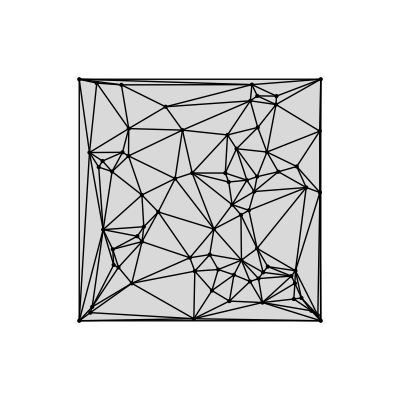

0.055817

```mathematica
t=AbsoluteTime[];
plotMechanism[m0]
AbsoluteTime[]-t
```

## periodic mechanisms

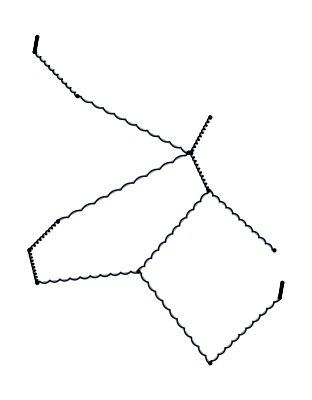
{0.159488,-Graphics-}

{0.00131,periodicIdentificationData[{1→15,2→14,7→5,9→15}]}

```mathematica
(m=minimalMechanism[randomCellNetwork[5],{{1,0},{0,1}}])//Timing
(pi=periodicIdentification[m,{{1,0},{0,1}}])//Timing
```

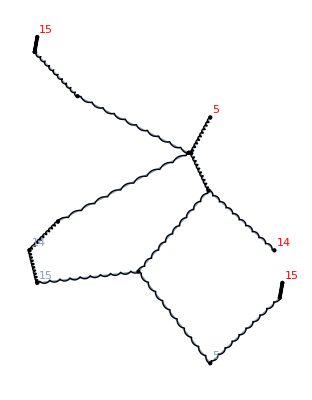

```mathematica
labelPeriodicVertices[m,pi]
```

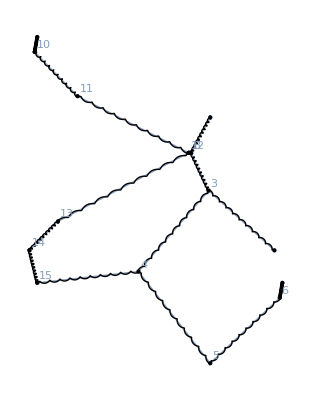

```mathematica
changeCellData[ joint,  pi["vertices"],"label"->pi["vertices"]]@m
```

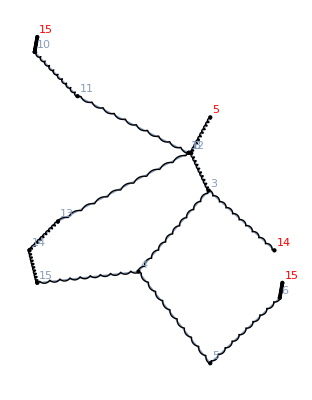

```mathematica
m2=changeCellData[ joint,  pi["vertices"],"label"->pi["vertices"]]@labelPeriodicVertices[m,pi]
```

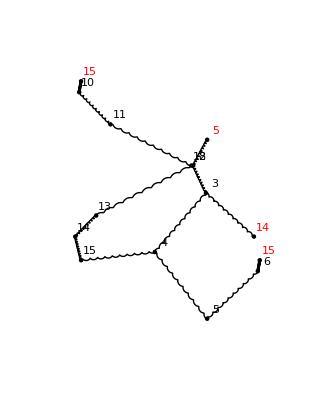

```mathematica
plotMechanism[m2]
```

```mathematica
vars=Flatten[vertexPosition[pi["vertices"],All[2]]];
hessian=D[mechanismEnergy[m]//.pi["positionRules"],{vars},{vars}]/.positionRules[m["positions"]];
```